```mathematica
Off[ClebschGordan::"tri"];
Off[SixJSymbol::"tri"];
(*PRD32,189-231(1985) Mesons in a relativized quark model with chromodynamics*)
(*计算所用参数*)
α={0.25,0.15,0.20};γ={1/2,√10/2,√1000/2};
mu=0.22;ms=0.419;mc=1.628;mb=4.977;mt=35;bconst=0.18;cconst=-0.253;σ0=1.8;s=1.55;ϵc=-0.168;ϵt=0.025;ϵsov=-0.035;ϵsos=0.055;
(*默认参数*)
r1=0.5;rmax=15;nmax=10;
(*自旋,轨道,张量项,smearing参数σ,τ*)
dspin[S_]:=1/2 S(S+1)-3/4;dso[S_,L_,J_]:=J(J+1)-L(L+1)-S(S+1);
dsqq[S_,L_,J_]:=If[S==0||L==0,0,Which[J==L+1,(J-1)/2,J==L,-1/2,J==L-1,(-J-2)/2]];
σij[m1_,m2_]:=√(σ0^2*(1/2+1/2((4m1*m2)/(m1+m2)^2)^4)+s^2((2m1*m2)/(m1+m2))^2);
τij[m1_,m2_,k_]:=√((γ[[k]]^2*σij[m1,m2]^2)/(γ[[k]]^2+σij[m1,m2]^2));
tensor[S_,L_,J_]:=If[S==0||L==0,0,Which[J==L+1,-(2(J-1))/(2J+1),J==L,2,J==L-1,-(2(J+2))/(2J+1)]];

Gtilde[m1_,m2_,r_]:=-∑_(k=1)^3 (4*α[[k]])/(3r)Erf[τij[m1,m2,k]*r];
Stilde[m1_,m2_,r_]:=bconst*r*(Exp[-σij[m1,m2]^2 r^2]/(√π σij[m1,m2]*r)+(1+1/(2 σij[m1,m2]^2*r^2))Erf[σij[m1,m2]*r])+cconst;
(*高斯基坐标和动量空间波函数*)
Nnl[i_,l_]:=((2^(l+2)(2νn[i])^(l+3/2))/(√π(2l+1)!!))^(1/2);
ϕr[i_,l_,r_]:=Nnl[i,l]*r^l*ⅇ^(-νn[i]*r^2);
ϕp[i_,l_,p_]:=Nnl[i,l]*1/(2νn[i])^(l+3/2)ⅇ^(-p^2/(4νn[i]))p^l;
(*计算势能项相关矩阵元,动量空间和坐标空间分开计算*)
pij[i_,j_,l_,m1_,m2_,ϵx_]:=NIntegrate[ϕp[i,l,p]*((m1*m2)/(√(p^2+m1^2)√(p^2+m2^2)))^(1/2+ϵx)*ϕp[j,l,p]*p^2,{p,0,∞}];
Gpij[i_,j_,l_,m1_,m2_]:=NIntegrate[ϕp[i,l,p]*(1+p^2/(√(p^2+m1^2)√(p^2+m2^2)))^(1/2)*ϕp[j,l,p]*p^2,{p,0,∞}];
Gtildeij[i_,j_,l_,m1_,m2_]:=NIntegrate[ϕr[i,l,r]*Gtilde[m1,m2,r]*ϕr[j,l,r]*r^2,{r,0,∞}];
Stildeij[i_,j_,l_,m1_,m2_]:=NIntegrate[ϕr[i,l,r]*Stilde[m1,m2,r]*ϕr[j,l,r]*r^2,{r,0,∞}];
Gij1[i_,j_,l_,m1_,m2_]:=NIntegrate[ϕr[i,l,r]*1/r*(D[Gtilde[m1,m2,rp],rp]/.rp->r)*ϕr[j,l,r]*r^2,{r,0,∞}];
Gij2[i_,j_,l_,m1_,m2_]:=NIntegrate[ϕr[i,l,r]*1/r^2(D[rp^2*D[Gtilde[m1,m2,rp],rp],rp]/.rp->r)*ϕr[j,l,r]*r^2,{r,0,∞}];
Gij3[i_,j_,l_,m1_,m2_]:=NIntegrate[ϕr[i,l,r]*(D[Gtilde[m1,m2,rp],{rp,2}]/.rp->r)*ϕr[j,l,r]*r^2,{r,0,∞}];
Sij[i_,j_,l_,m1_,m2_]:=NIntegrate[ϕr[i,l,r]*1/r*(D[Stilde[m1,m2,rp],rp]/.rp->r)*ϕr[j,l,r]*r^2,{r,0,∞}];

mon[i_,j_,l_,m1_,m2_]:=NIntegrate[ϕp[i,l,p]*(√(p^2+m1^2)+√(p^2+m2^2))*ϕp[j,l,p]*p^2,{p,0,∞}];
Eij[i_,j_,l_]:=((2 √(νn[i]νn[j]))/(νn[i]+νn[j]))^(l+3/2);
(*求解本征方程:Sol函数,返回本征值.
*)
Sol[n1_,l1_,S1_,J1_,m11_,m21_,r11_,rmax1_,nmax1_,zz1_]:=Module[{n=n1,l=l1,S=S1,J=J1,m1=m11,m2=m21,r1=r11,rmax=rmax1,nmax=nmax1,zz=zz1},acon=(rmax/r1)^(1/(nmax-1));νn[i_]:=1/((r1*acon^(i-1))^2);
(*势能项矩阵*)
mat1=Table[pij[i,j,l,m1,m1,ϵsov],{i,1,nmax},{j,1,nmax}];
mat2=Table[pij[i,j,l,m2,m2,ϵsov],{i,1,nmax},{j,1,nmax}];
mat3=Table[pij[i,j,l,m1,m2,ϵsov],{i,1,nmax},{j,1,nmax}];
mat4=Table[pij[i,j,l,m1,m2,ϵc],{i,1,nmax},{j,1,nmax}];
mat5=Table[pij[i,j,l,m1,m2,ϵt],{i,1,nmax},{j,1,nmax}];
mat6=Table[pij[i,j,l,m1,m1,ϵsos],{i,1,nmax},{j,1,nmax}];
mat7=Table[pij[i,j,l,m2,m2,ϵsos],{i,1,nmax},{j,1,nmax}];
mat8=Table[Gpij[i,j,l,m1,m2],{i,1,nmax},{j,1,nmax}];
mat9=Table[Gtildeij[i,j,l,m1,m2],{i,1,nmax},{j,1,nmax}];
mat10=Table[Stildeij[i,j,l,m1,m2],{i,1,nmax},{j,1,nmax}];
mat11=Table[Gij1[i,j,l,m1,m2],{i,1,nmax},{j,1,nmax}];
mat12=Table[Gij2[i,j,l,m1,m2],{i,1,nmax},{j,1,nmax}];
mat13=Table[Gij3[i,j,l,m1,m2],{i,1,nmax},{j,1,nmax}];
mat14=Table[Sij[i,j,l,m1,m2],{i,1,nmax},{j,1,nmax}];
(*动能矩阵*)
tt=Table[mon[i,j,l,m1,m2],{i,1,nmax},{j,1,nmax}];
te=Table[Eij[i,j,l],{i,1,nmax},{j,1,nmax}];
tein=Inverse[te];
(*H=T+V*)
th=tt+mat8.tein.mat9.tein.mat8+dsqq[S,l,J]/(2 m1^2)*mat1.tein.mat11.tein.mat1+dsqq[S,l,J]/(2 m2^2)*mat2.tein.mat11.tein.mat2+(2dsqq[S,l,J])/(m1*m2)*mat3.tein.mat11.tein.mat3+(2dspin[S])/(3m1*m2)*mat4.tein.mat12.tein.mat4-1/12*tensor[S,l,J]/(m1*m2)(mat5.tein.mat13.tein.mat5-mat5.tein.mat11.tein.mat5)+mat10-(dsqq[S,l,J]/(2 m1^2)*mat6.tein.mat14.tein.mat6+dsqq[S,l,J]/(2 m2^2)*mat7.tein.mat14.tein.mat7);
(*求解本征值和本征向量,得到波函数*)
{Ed,wave}=Eigensystem[{th,te}];
en=Ed[[-(n+1)]];
tb=Table[√(2νn[i]),{i,nmax}];
coabc=Sign[∑_(i=1)^nmax wave[[-(n+1)]][[i]]*ϕr[i,l,0.1]]*(wave[[-(n+1)]].te.wave[[-(n+1)]])^(-1/2)*wave[[-(n+1)]];
unr[n_,l_,r_]:=∑_(i=1)^nmax coabc[[i]]*ϕr[i,l,r]*r;

(*输出能量,画图*)
If[zz==0,Print["Eigenvalue = ",en];
Print[Plot[unr[n,l,r],{r,0,10}]]];Return[unr[n,l,r]]];
```

## Results

```mathematica
<<MaTeX`
```

#### J/ψ

Eigenvalue = 3.09138

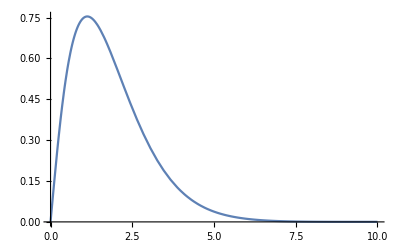

```mathematica
n1=0;l1=0;S1=1;J1=0;m11=mc;m21=mc;
psi[r_]=Sol[n1,l1,S1,J1,m11,m21,r1,rmax,nmax,0];
```

#### ψ(2S)

Eigenvalue = 3.67913

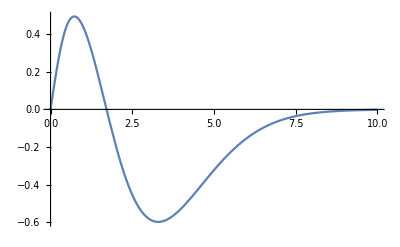

```mathematica
n1=1;l1=0;S1=1;J1=0;m11=mc;m21=mc;
psi2[r_]=Sol[n1,l1,S1,J1,m11,m21,r1,rmax,nmax,0];
```

### Wavefuction

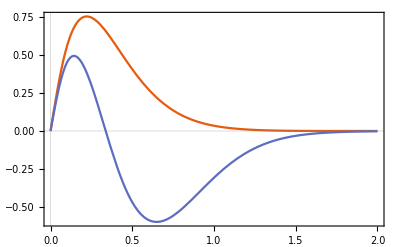

```mathematica
Plot[{psi[r/0.197],psi2[r/0.197]},{r,0,2},Frame->True,PlotTheme->"Scientific",FrameLabel->{MaTeX["r({\\rm fm})"],MaTeX["\\psi(r)"]},PlotLegends->{MaTeX["J/\\psi"],MaTeX["\\psi(2S)"]}]
```

### Check Orthonormal

```mathematica
NIntegrate[psi[r]^2,{r,0,Infinity}]
NIntegrate[psi2[r]^2,{r,0,Infinity}]
NIntegrate[psi[r]*psi2[r],{r,0,Infinity}]//Quiet
```

1.

1.

1.3522×10^-13

### Momentum emission

Naively thinking, ππ emission with 3-momentum q from charmonia can be simply treated as the momentum loss of one c quark. The coupling of ψψππ should be proportional to the inner production of the initial and final states of charmonia. After the loss of momentum q, the state becomes |ψ_f> = e^(i q r)|ψ_i> and then the coupling  ∝<ψ_f|ψ_i> =∫d r (ψ_f(r))^*ψ_i(r)(sin(q r))/(q r)

```mathematica
c12[q_]:=NIntegrate[psi[r]psi2[r]*Sin[q r/2]/(q r/2),{r,0,20}]
c11[q_]:=NIntegrate[psi[r]psi[r]*Sin[q r/2]/(q r/2),{r,0,20}]
c22[q_]:=NIntegrate[psi2[r]psi2[r]*Sin[q r/2]/(q r/2),{r,0,20}]
```

```mathematica
texStyle={FontFamily->"Latin Modern Roman",FontSize->10};
```

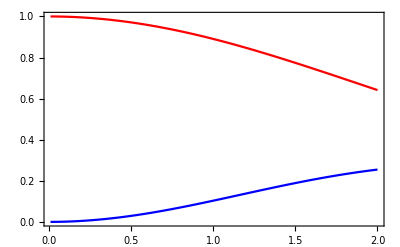

```mathematica
Plot[{c11[q],(*c22[q],*)c12[q]},{q,0.01,2},Frame->True,FrameLabel->{MaTeX["q(\\rm GeV)"]},PlotLegends->Placed[{MaTeX["I_{J/\\psi J/\\psi}",FontSize->14](*,MaTeX["I_{\\psi(2S) \\psi(2S)}",FontSize->14]*),MaTeX["I_{\\psi(2S)J/\\psi}",FontSize->14]},{0.2,0.5}],BaseStyle->texStyle,LabelStyle->{12,GrayLevel[-2]},PlotStyle->{Red,Blue(*,Green*)}]
```

```mathematica
Table[c11[q],{q,0,2,0.1}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,20}}.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,20}}.

{NIntegrate[(psi[r] psi[r] Sin[(0. r)/2])/((0. r)/2),{r,0,20}],0.998826,0.995313,0.989492,0.981414,0.97115,0.958786,0.944428,0.928195,0.910217,0.890639,0.869612,0.847293,0.823845,0.799432,0.774218,0.748364,0.72203,0.695368,0.668523,0.641635}

```mathematica
Table[c12[q],{q,0,2,0.1}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,20}}.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,20}}.

{NIntegrate[(psi[r] psi2[r] Sin[(0. r)/2])/((0. r)/2),{r,0,20}],0.00121947,0.00485288,0.010826,0.0190177,0.0292629,0.0413583,0.0550669,0.0701257,0.086252,0.103151,0.120523,0.138073,0.155511,0.172567,0.188989,0.20455,0.219054,0.232334,0.244255,0.254715}

```mathematica
Table[q,{q,0,2,0.1}]
```

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.}

```mathematica
qmax=1;
NIntegrate[q^2 c11[q],{q,0.01,qmax}]/NIntegrate[q^2 c12[q],{q,0.01,qmax}]//Quiet
```

14.3599

```mathematica
NIntegrate[c12[q],{q,0.01,2}]
```

NIntegrate::inumr: The integrand (2 («1») (0.074128 ⅇ^(-4. r^2) r+0.163519 ⅇ^(-1.8785 r^2) r+0.259533 ⅇ^(-0.882189 r^2) r+«5»+0.00105734 ⅇ^(-0.0201519 r^2) r-0.000227125 ⅇ^(-0.00946382 r^2) r+0.0000297804 ⅇ^(-0.00444444 r^2) r) Sin[(q r)/2])/(q r) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,20}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

0.222354

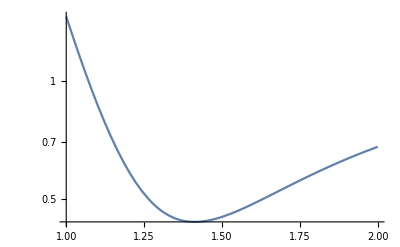

```mathematica
LogPlot[c11[r]*c22[r]/c12[r]^2,{r,1,2}]
```

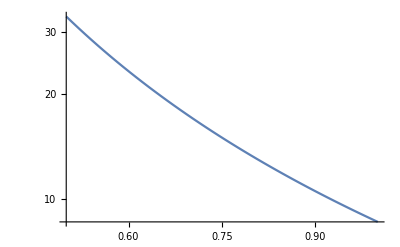

```mathematica
LogPlot[c11[r]/c12[r],{r,0.5,1}]
```

```mathematica
D[x (E^{-(x+m^2)/l^2})/(x+m^2),x]//Simplify
```

{(ⅇ^(-(m^2+x)/l^2) (l^2 m^2-x (m^2+x)))/(l^2 (m^2+x)^2)}

```mathematica
Solve[(l^2 m^2-x (m^2+x))==0,x]//Simplify
```

{{x→1/2 (-m^2-√(4 l^2 m^2+m^4))},{x→1/2 (-m^2+√(4 l^2 m^2+m^4))}}

```mathematica
1/2 (-m^2+√(4 l^2 m^2+m^4))/.m->0.8/.l->1
```

0.541626

```mathematica
Manipulate[Plot[x^2 (E^{-(x^2+m^2)/l^2})/(x^2+m^2),{x,0,2}],{l,1,3},{m,0.5,0.8}]
```